```mathematica
mySqrt[X_]=-I*Sqrt[-X];
```

```mathematica
G := Inverse[{{z-J-q*Cos[k],-q*Cos[k]},{-q*Cos[k],-z-J-q*Cos[k]}}-c*(((Cos[k]-1)p/4*{{1,1},{1,1}}.Inverse[{{1-p/4(1/(2J*q)-(J^2-z^2)/(2J*q*a)-1/a)(z+J),(z-J)p/4(1/(2J*q)-(J^2-z^2)/(2J*q*a)-1/a)},{-(z+J)p/4(1/(2J*q)-(J^2-z^2)/(2J*q*a)-1/a),1+(z-J)p/4(1/(2J*q)-(J^2-z^2)/(2J*q*a)-1/a)}}]+p/4(Cos[k]+1)*{{1,1},{1,1}}.Inverse[{{1-p/4(1/(2J*q)-(J^2-z^2)/(2J*q*a)+1/a)(z+J),(z-J)p/4(1/(2J*q)-(J^2-z^2)/(2J*q*a)+1/a)},{-(z+J)p/4(1/(2J*q)-(J^2-z^2)/(2J*q*a)+1/a),1+(z-J)p/4(1/(2J*q)-(J^2-z^2)/(2J*q*a)+1/a)}}]))]
```

```mathematica
G2 := G/.{a->mySqrt[(J^2-z^2)^2-(2*J*q)^2]}
```

```mathematica
Gf := G2/.{J->1,q->0.1,p->0.05, c->0.01, z->z+I*n}
```

```mathematica
Gf
```

{{(-1-ⅈ n-z-0.1 Cos[k]-0.01 (0.125 (-(0.125 (-1+ⅈ n+z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1-0.125 (1+ⅈ n+z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (-1+Cos[k])+0.125 (-(0.125 (-1+ⅈ n+z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1-0.125 (1+ⅈ n+z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (1+Cos[k])))/(-((-0.1 Cos[k]-0.01 (0.125 (-(0.125 (-1-ⅈ n-z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1+0.125 (-1+ⅈ n+z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (-1+Cos[k])+0.125 (-(0.125 (-1-ⅈ n-z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1+0.125 (-1+ⅈ n+z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (1+Cos[k]))) (-0.1 Cos[k]-0.01 (0.125 (-(0.125 (-1+ⅈ n+z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1-0.125 (1+ⅈ n+z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (-1+Cos[k])+0.125 (-(0.125 (-1+ⅈ n+z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1-0.125 (1+ⅈ n+z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (1+Cos[k]))))+(-1+ⅈ n+z-0.1 Cos[k]-0.01 (0.125 (-(0.125 (-1-ⅈ n-z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1+0.125 (-1+ⅈ n+z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (-1+Cos[k])+0.125 (-(0.125 (-1-ⅈ n-z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1+0.125 (-1+ⅈ n+z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (1+Cos[k]))) (-1-ⅈ n-z-0.1 Cos[k]-0.01 (0.125 (-(0.125 (-1+ⅈ n+z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1-0.125 (1+ⅈ n+z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (-1+Cos[k])+0.125 (-(0.125 (-1+ⅈ n+z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1-0.125 (1+ⅈ n+z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (1+Cos[k])))),(0.1 Cos[k]+0.01 (0.125 (-(0.125 (-1+ⅈ n+z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1-0.125 (1+ⅈ n+z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (-1+Cos[k])+0.125 (-(0.125 (-1+ⅈ n+z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1-0.125 (1+ⅈ n+z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (1+Cos[k])))/(-((-0.1 Cos[k]-0.01 (0.125 (-(0.125 (-1-ⅈ n-z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1+0.125 (-1+ⅈ n+z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (-1+Cos[k])+0.125 (-(0.125 (-1-ⅈ n-z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1+0.125 (-1+ⅈ n+z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (1+Cos[k]))) (-0.1 Cos[k]-0.01 (0.125 (-(0.125 (-1+ⅈ n+z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1-0.125 (1+ⅈ n+z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (-1+Cos[k])+0.125 (-(0.125 (-1+ⅈ n+z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1-0.125 (1+ⅈ n+z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (1+Cos[k]))))+(-1+ⅈ n+z-0.1 Cos[k]-0.01 (0.125 (-(0.125 (-1-ⅈ n-z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1+0.125 (-1+ⅈ n+z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (-1+Cos[k])+0.125 (-(0.125 (-1-ⅈ n-z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1+0.125 (-1+ⅈ n+z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (1+Cos[k]))) (-1-ⅈ n-z-0.1 Cos[k]-0.01 (0.125 (-(0.125 (-1+ⅈ n+z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1-0.125 (1+ⅈ n+z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (-1+Cos[k])+0.125 (-(0.125 (-1+ⅈ n+z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1-0.125 (1+ⅈ n+z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (1+Cos[k]))))},{(0.1 Cos[k]+0.01 (0.125 (-(0.125 (-1-ⅈ n-z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1+0.125 (-1+ⅈ n+z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (-1+Cos[k])+0.125 (-(0.125 (-1-ⅈ n-z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1+0.125 (-1+ⅈ n+z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (1+Cos[k])))/(-((-0.1 Cos[k]-0.01 (0.125 (-(0.125 (-1-ⅈ n-z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1+0.125 (-1+ⅈ n+z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (-1+Cos[k])+0.125 (-(0.125 (-1-ⅈ n-z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1+0.125 (-1+ⅈ n+z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (1+Cos[k]))) (-0.1 Cos[k]-0.01 (0.125 (-(0.125 (-1+ⅈ n+z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1-0.125 (1+ⅈ n+z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (-1+Cos[k])+0.125 (-(0.125 (-1+ⅈ n+z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1-0.125 (1+ⅈ n+z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (1+Cos[k]))))+(-1+ⅈ n+z-0.1 Cos[k]-0.01 (0.125 (-(0.125 (-1-ⅈ n-z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1+0.125 (-1+ⅈ n+z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (-1+Cos[k])+0.125 (-(0.125 (-1-ⅈ n-z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1+0.125 (-1+ⅈ n+z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (1+Cos[k]))) (-1-ⅈ n-z-0.1 Cos[k]-0.01 (0.125 (-(0.125 (-1+ⅈ n+z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1-0.125 (1+ⅈ n+z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (-1+Cos[k])+0.125 (-(0.125 (-1+ⅈ n+z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1-0.125 (1+ⅈ n+z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (1+Cos[k])))),(-1+ⅈ n+z-0.1 Cos[k]-0.01 (0.125 (-(0.125 (-1-ⅈ n-z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1+0.125 (-1+ⅈ n+z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (-1+Cos[k])+0.125 (-(0.125 (-1-ⅈ n-z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1+0.125 (-1+ⅈ n+z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (1+Cos[k])))/(-((-0.1 Cos[k]-0.01 (0.125 (-(0.125 (-1-ⅈ n-z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1+0.125 (-1+ⅈ n+z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (-1+Cos[k])+0.125 (-(0.125 (-1-ⅈ n-z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1+0.125 (-1+ⅈ n+z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (1+Cos[k]))) (-0.1 Cos[k]-0.01 (0.125 (-(0.125 (-1+ⅈ n+z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1-0.125 (1+ⅈ n+z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (-1+Cos[k])+0.125 (-(0.125 (-1+ⅈ n+z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1-0.125 (1+ⅈ n+z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (1+Cos[k]))))+(-1+ⅈ n+z-0.1 Cos[k]-0.01 (0.125 (-(0.125 (-1-ⅈ n-z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1+0.125 (-1+ⅈ n+z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (-1+Cos[k])+0.125 (-(0.125 (-1-ⅈ n-z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1+0.125 (-1+ⅈ n+z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (1+Cos[k]))) (-1-ⅈ n-z-0.1 Cos[k]-0.01 (0.125 (-(0.125 (-1+ⅈ n+z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1-0.125 (1+ⅈ n+z) (5.-ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (-1+Cos[k])+0.125 (-(0.125 (-1+ⅈ n+z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))+(1-0.125 (1+ⅈ n+z) (5.+ⅈ/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04-(1-(ⅈ n+z)^2)^2)))) (1+Cos[k]))))}}

```mathematica
Gfinal := (-1-ⅈ n-z-0.1 Cos[k]-0.01 (0.125 (-(0.125 (-1+ⅈ n+z) (5.-ⅈ/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2)))+(1-0.125 (1+ⅈ n+z) (5.-ⅈ/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2)))) (-1+Cos[k])+0.125 (-(0.125 (-1+ⅈ n+z) (5.+ⅈ/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2)))+(1-0.125 (1+ⅈ n+z) (5.+ⅈ/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2)))) (1+Cos[k])))/(-((-0.1 Cos[k]-0.01 (0.125 (-(0.125 (-1-ⅈ n-z) (5.-ⅈ/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2)))+(1+0.125 (-1+ⅈ n+z) (5.-ⅈ/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2)))) (-1+Cos[k])+0.125 (-(0.125 (-1-ⅈ n-z) (5.+ⅈ/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2)))+(1+0.125 (-1+ⅈ n+z) (5.+ⅈ/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2)))) (1+Cos[k]))) (-0.1 Cos[k]-0.01 (0.125 (-(0.125 (-1+ⅈ n+z) (5.-ⅈ/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2)))+(1-0.125 (1+ⅈ n+z) (5.-ⅈ/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2)))) (-1+Cos[k])+0.125 (-(0.125 (-1+ⅈ n+z) (5.+ⅈ/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2)))+(1-0.125 (1+ⅈ n+z) (5.+ⅈ/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2)))) (1+Cos[k]))))+(-1+ⅈ n+z-0.1 Cos[k]-0.01 (0.125 (-(0.125 (-1-ⅈ n-z) (5.-ⅈ/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2)))+(1+0.125 (-1+ⅈ n+z) (5.-ⅈ/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2)))) (-1+Cos[k])+0.125 (-(0.125 (-1-ⅈ n-z) (5.+ⅈ/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2)))+(1+0.125 (-1+ⅈ n+z) (5.+ⅈ/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2)))) (1+Cos[k]))) (-1-ⅈ n-z-0.1 Cos[k]-0.01 (0.125 (-(0.125 (-1+ⅈ n+z) (5.-ⅈ/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2)))+(1-0.125 (1+ⅈ n+z) (5.-ⅈ/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2)))) (-1+Cos[k])+0.125 (-(0.125 (-1+ⅈ n+z) (5.+ⅈ/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2)))+(1-0.125 (1+ⅈ n+z) (5.+ⅈ/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+5. ⅈ) (1-(ⅈ n+z)^2))/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))))/(-0.25+(0.+1. ⅈ)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2))-((0.+1.25 ⅈ) (ⅈ n+z)^2)/(√(0.04000000000000001-(1-(ⅈ n+z)^2)^2)))) (1+Cos[k]))))/.{n->0.006}
```

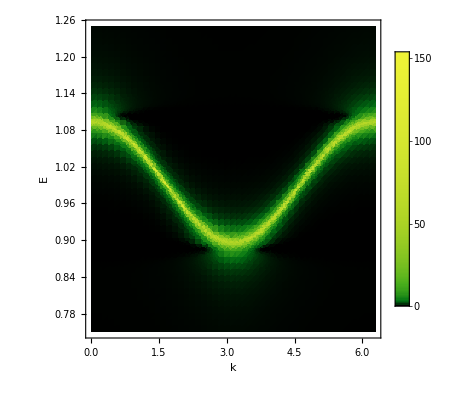

```mathematica
DensityPlot[-1/Pi Im[Gfinal],{k,0,2*Pi}, {z,0.75,1.25},AxesLabel->{"k","E"}, Exclusions->None, PlotLegends->Automatic, ColorFunction->(ColorData["AvocadoColors"][Log[1+#]/Log[200]]&), ColorFunctionScaling->False, PlotRange->All, PlotPoints->50]
```

```mathematica
Gcut = Gfinal/.{k->Pi}
```

((-0.9-0.006 ⅈ)-z-0.01 (0.-0.25 (-(0.125 ((-1.+0.006 ⅈ)+z) (5.-ⅈ/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+5. ⅈ) (1-((0.+0.006 ⅈ)+z)^2))/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+1.25 ⅈ) ((0.+0.006 ⅈ)+z)^2)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2)))+(1-0.125 ((1.+0.006 ⅈ)+z) (5.-ⅈ/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+5. ⅈ) (1-((0.+0.006 ⅈ)+z)^2))/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+1.25 ⅈ) ((0.+0.006 ⅈ)+z)^2)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))))))/(-((0.1-0.01 (0.-0.25 (-(0.125 ((-1.-0.006 ⅈ)-z) (5.-ⅈ/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+5. ⅈ) (1-((0.+0.006 ⅈ)+z)^2))/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+1.25 ⅈ) ((0.+0.006 ⅈ)+z)^2)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2)))+(1+0.125 ((-1.+0.006 ⅈ)+z) (5.-ⅈ/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+5. ⅈ) (1-((0.+0.006 ⅈ)+z)^2))/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+1.25 ⅈ) ((0.+0.006 ⅈ)+z)^2)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2)))))) (0.1-0.01 (0.-0.25 (-(0.125 ((-1.+0.006 ⅈ)+z) (5.-ⅈ/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+5. ⅈ) (1-((0.+0.006 ⅈ)+z)^2))/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+1.25 ⅈ) ((0.+0.006 ⅈ)+z)^2)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2)))+(1-0.125 ((1.+0.006 ⅈ)+z) (5.-ⅈ/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+5. ⅈ) (1-((0.+0.006 ⅈ)+z)^2))/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+1.25 ⅈ) ((0.+0.006 ⅈ)+z)^2)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2)))))))+((-0.9+0.006 ⅈ)+z-0.01 (0.-0.25 (-(0.125 ((-1.-0.006 ⅈ)-z) (5.-ⅈ/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+5. ⅈ) (1-((0.+0.006 ⅈ)+z)^2))/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+1.25 ⅈ) ((0.+0.006 ⅈ)+z)^2)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2)))+(1+0.125 ((-1.+0.006 ⅈ)+z) (5.-ⅈ/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+5. ⅈ) (1-((0.+0.006 ⅈ)+z)^2))/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+1.25 ⅈ) ((0.+0.006 ⅈ)+z)^2)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2)))))) ((-0.9-0.006 ⅈ)-z-0.01 (0.-0.25 (-(0.125 ((-1.+0.006 ⅈ)+z) (5.-ⅈ/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+5. ⅈ) (1-((0.+0.006 ⅈ)+z)^2))/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+1.25 ⅈ) ((0.+0.006 ⅈ)+z)^2)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2)))+(1-0.125 ((1.+0.006 ⅈ)+z) (5.-ⅈ/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+5. ⅈ) (1-((0.+0.006 ⅈ)+z)^2))/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))))/(-0.25+(0.+1.5 ⅈ)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2))-((0.+1.25 ⅈ) ((0.+0.006 ⅈ)+z)^2)/(√(0.04-(1-((0.+0.006 ⅈ)+z)^2)^2)))))))

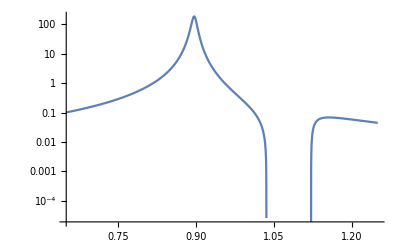

```mathematica
LogPlot[-Im[Gcut],{z,0.65,1.25}]
```